/home/hemant/Desktop/code/dna/Nucleation_6/results/Intact

{{},{L:,20.},{m:,40},{N:,5},{eta_b:,2.},{kappa_sigma_r:,1.},{Delta:,0.2469},{},{Extension Minimum:,0},{Extension Maximum:,25},{TOLERANCE:,0.}}

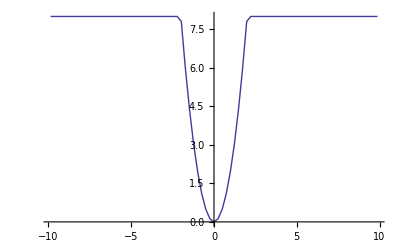

```mathematica
Needs["PlotLegends`"]
SetDirectory[FileNameJoin[{NotebookDirectory[]}]]
Parameters=Import["../Parameters"]
Potential=Import["../POTENTIAL_DATA","Table"];
ListLinePlot[Potential,PlotStyle->{Thick},PlotRange->All]

IntactPF=Import["PartitionFunction_0_0.out","Table"];
IntactFE=Import["FreeEnergy_0_0.out","Table"];
IntactdFE=Import["dFreeEnergy_0_0.out","Table"];

IntactZNJη=Import["znj_eta.out","Table"];
IntactZNJξ=Import["znj_xi.out","Table"];

IntactMXDη=Import["MeanAxialDisp_eta.out","Table"];
IntactMXDξ=Import["MeanAxialDisp_xi.out","Table"];

AverageX= Import["Average_X.out","Table"];
AverageY= Import["Average_Y.out","Table"];

fsTitle=24;
fsAxesLabel=18;
fs2=16;

n=Parameters[[4,2]];
Δ=Parameters[[7,2]];
umin=Parameters[[9,2]]+1;
umax=Parameters[[10,2]]+1;
```

## Numerical Results

### Partition Function

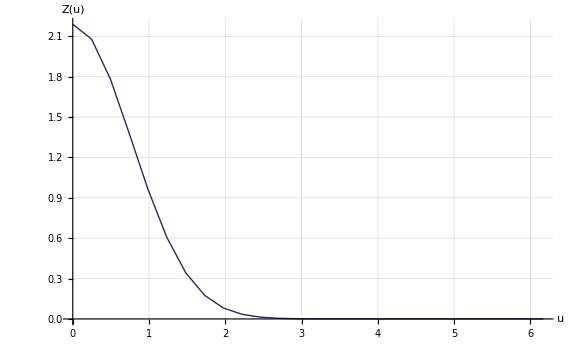

```mathematica
pIntactPF=ListLinePlot[
IntactPF,
ImageSize->Large,
PlotStyle->{Thick,Darker[ColorData[1,1]]},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesOrigin->{0,0},
PlotRange->All,
AxesLabel->{
Style["u",FontSize->fsAxesLabel],
Style["Z(u)",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2}
]
```

### Free Energy

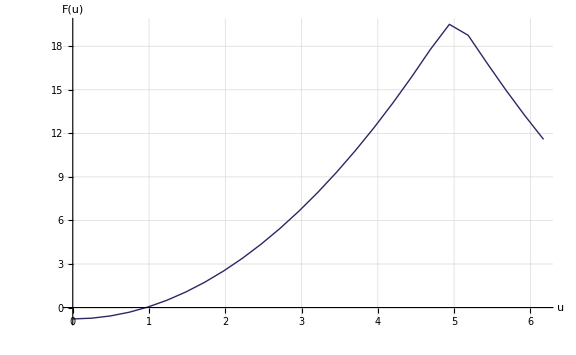

```mathematica
pIntactPF=ListLinePlot[
IntactFE,
ImageSize->Large,
PlotStyle->{Thick,Darker[ColorData[1,1]]},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesOrigin->{0,0},
PlotRange->All,
AxesLabel->{
Style["u",FontSize->fsAxesLabel],
Style["F(u)",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2}
]
```

### Force-Extension

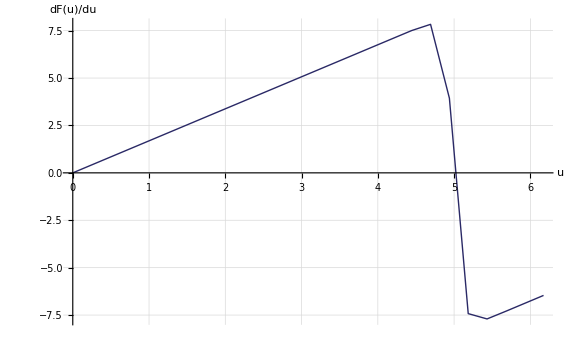

```mathematica
pIntactPF=ListLinePlot[
IntactdFE,
ImageSize->Large,
PlotStyle->{Thick,Darker[ColorData[1,1]]},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesOrigin->{0,0},
PlotRange->All,
AxesLabel->{
Style["u",FontSize->fsAxesLabel],
Style["dF(u)/du",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2}
]
```

### Mean Axial Displacement of ξ and η

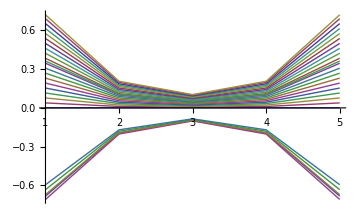
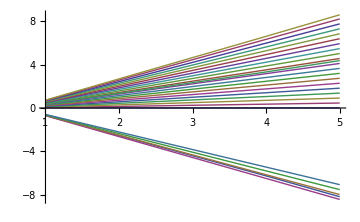

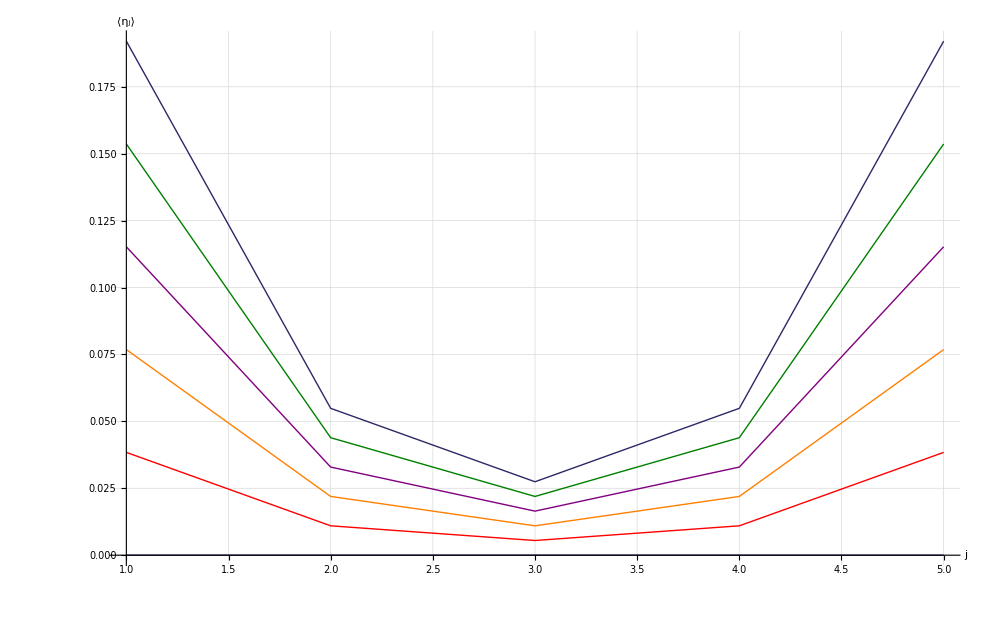

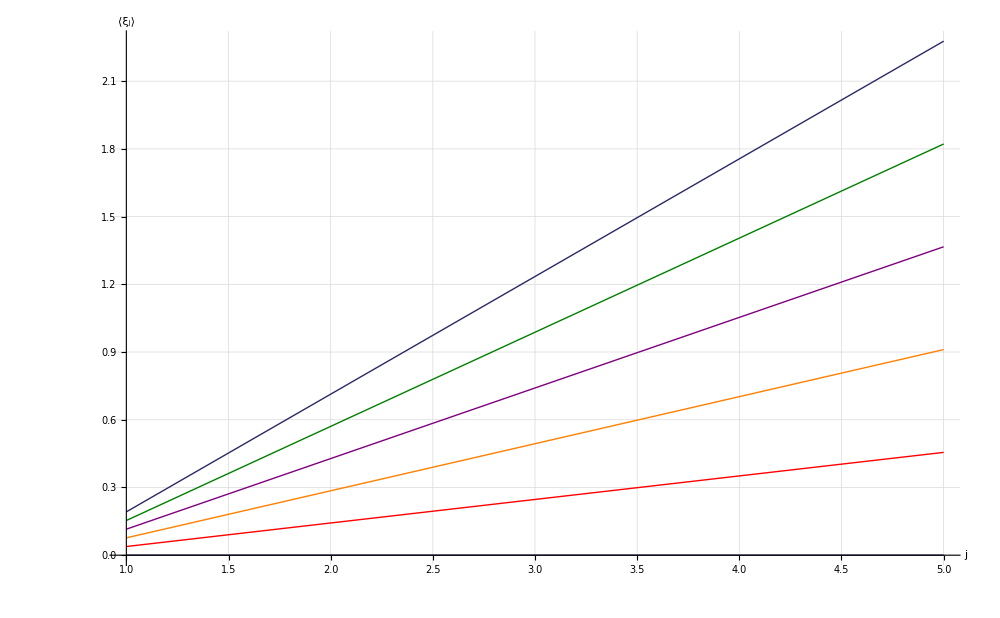

```mathematica
{ListLinePlot[IntactMXDη,PlotStyle->Thick,ImageSize->Medium,AxesOrigin->{1,0}],
ListLinePlot[IntactMXDξ,PlotStyle->Thick,ImageSize->Medium,AxesOrigin->{1,0}]}
pIntactMXDη=ListLinePlot[
{
IntactMXDη[[1]],
IntactMXDη[[2]],
IntactMXDη[[3]],
IntactMXDη[[4]],
IntactMXDη[[5]],
IntactMXDη[[6]]
},
ImageSize->{1000,600},
PlotStyle->{
{Thick,Darker[ColorData[1,1]]},
{Thick,Red},
{Thick,Orange},
{Thick,Purple},
{Thick,Darker[Green,0.5]}
},
PlotLegend->{
Style["u=0",FontSize->fs2],
Style["u="<>ToString[1Δ],FontSize->fs2],
Style["u="<>ToString[2Δ],FontSize->fs2],
Style["u="<>ToString[3Δ],FontSize->fs2],
Style["u="<>ToString[4Δ],FontSize->fs2],
Style["u="<>ToString[5Δ],FontSize->fs2]
},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
PlotRange->All,
AxesOrigin->{1,0},
AxesLabel->{
Style["j",FontSize->fsAxesLabel],
Style["⟨η_j⟩",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2},
LegendShadow->None,
LegendBorder->None,
LegendBackground->Opacity[0],
ShadowBackground->Opacity[0],
LegendSize->0.55,
LegendPosition->{0.9,-.2}
]

pIntactMXDξ=ListLinePlot[
{
IntactMXDξ[[1]],
IntactMXDξ[[2]],
IntactMXDξ[[3]],
IntactMXDξ[[4]],
IntactMXDξ[[5]],
IntactMXDξ[[6]]
},
ImageSize->{1000,600},
PlotStyle->{
{Thick,Darker[ColorData[1,1]]},
{Thick,Red},
{Thick,Orange},
{Thick,Purple},
{Thick,Darker[Green,0.5]}
},
PlotLegend->{
Style["u=0",FontSize->fs2],
Style["u="<>ToString[1Δ],FontSize->fs2],
Style["u="<>ToString[2Δ],FontSize->fs2],
Style["u="<>ToString[3Δ],FontSize->fs2],
Style["u="<>ToString[4Δ],FontSize->fs2],
Style["u="<>ToString[5Δ],FontSize->fs2]
},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
PlotRange->All,
AxesOrigin->{1,0},
AxesLabel->{
Style["j",FontSize->fsAxesLabel],
Style["⟨ξ_j⟩",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2},
LegendShadow->None,
LegendBorder->None,
LegendBackground->Opacity[0],
ShadowBackground->Opacity[0],
LegendSize->0.55,
LegendPosition->{0.9,-.2}
]
```

### Average X and Y

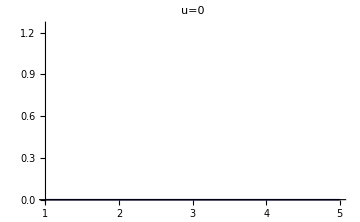
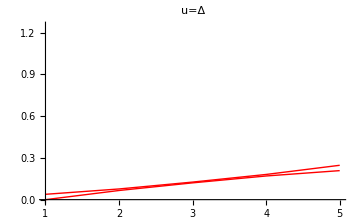
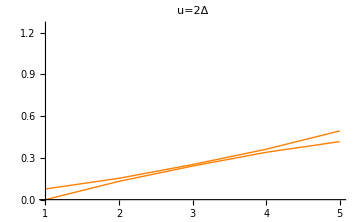
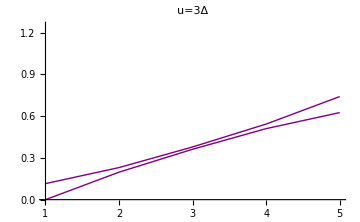
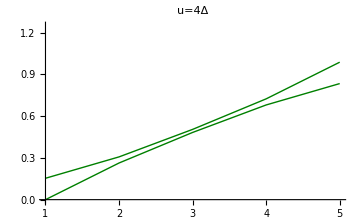
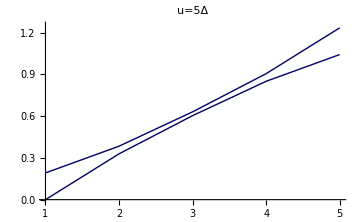

```mathematica
{ListLinePlot[{Chop[AverageX[[1]]],Chop[AverageY[[1]]]},AxesOrigin->{1,0},PlotStyle->{{Thick,Darker[Blue,0.6]}},PlotRange->{{1,5},{0,1.25}},PlotLabel->"u=0",ImageSize->Medium],
ListLinePlot[{AverageX[[2]],AverageY[[2]]},AxesOrigin->{1,0},PlotStyle->{{Thick,Red}},PlotRange->{{1,5},{0,1.25}},PlotLabel->"u=Δ",ImageSize->Medium],
ListLinePlot[{AverageX[[3]],AverageY[[3]]},AxesOrigin->{1,0},PlotStyle->{{Thick,Orange}},PlotRange->{{1,5},{0,1.25}},PlotLabel->"u=2Δ",ImageSize->Medium],
ListLinePlot[{AverageX[[4]],AverageY[[4]]},AxesOrigin->{1,0},PlotStyle->{{Thick,Purple}},PlotRange->{{1,5},{0,1.25}},PlotLabel->"u=3Δ",ImageSize->Medium],
ListLinePlot[{AverageX[[5]],AverageY[[5]]},AxesOrigin->{1,0},PlotStyle->{{Thick,Darker[Green,0.5]}},PlotRange->{{1,5},{0,1.25}},PlotLabel->"u=4Δ",ImageSize->Medium],
ListLinePlot[{AverageX[[6]],AverageY[[6]]},AxesOrigin->{1,0},PlotStyle->{{Thick,Darker[Blue,0.6]}},PlotRange->{{1,5},{0,1.25}},PlotLabel->"u=5Δ",ImageSize->Medium]}
```